```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 181 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
Clear[F] 
F = -(k/𝓇^2)+ K/𝓇^3
```

K/𝓇^3-k/𝓇^2

```mathematica
Integrate[- F , { 𝓇 , ∞ , r } ]
```

ConditionalExpression[(K-2 k r)/(2 r^2), Im[r]≠0||Re[r]>0]

```mathematica
Clear[𝒱]
𝒱 = 
Assuming[ 
Im[r]≠0||Re[r]>0 , 
Integrate[- F , { 𝓇 , ∞ , r } ] ]
```

(K-2 k r)/(2 r^2)

```mathematica
𝒱 // Apart
```

K/(2 r^2)-k/r

```mathematica
D[𝒱, r] // Apart
```

-K/r^3+k/r^2

```mathematica
( D[𝒱, r] /. r -> r[t] )  // Apart
```

-K/r[t]^3+k/r[t]^2

```mathematica
Clear[s]
s = { r[t] Cos[θ[t]] , r[t] Sin[θ[t]] }
```

{Cos[θ[t]] r[t],r[t] Sin[θ[t]]}

```mathematica
D[s, t]
```

{Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t],Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

(Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t])^2+(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

Cos[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 r'[t]^2+Cos[θ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand  // Simplify
```

r'[t]^2+r[t]^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[s, t] . D[s, t]  // Expand  // Simplify )
```

1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
Clear[q]
q = { r[t] , θ[t] }
```

{r[t],θ[t]}

```mathematica
Clear[V]
V = 𝒱 /. r -> r[t] // Apart
```

K/(2 r[t]^2)-k/r[t]

```mathematica
Clear[ℒ]
ℒ = T - V
```

-K/(2 r[t]^2)+k/r[t]+1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] == 0  
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ] == 0  // Simplify
```

-K/r[t]^3+k/r[t]^2-m r[t] θ'[t]^2+m r''[t]==0

m r[t] (2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

K/r[t]^3-k/r[t]^2+m r[t] θ'[t]^2-m r''[t]==0
-m r[t] (2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[com]
com = 
FirstIntegrals[ ℒ , q, t ]
```

{FirstIntegral[θ]→-m r[t]^2 θ'[t],FirstIntegral[t]→(K-2 k r[t]+m r[t]^2 r'[t]^2+m r[t]^4 θ'[t]^2)/(2 r[t]^2)}

```mathematica
Clear[parameters]
parameters = { 
K -> 10 , 
k -> 10 , 
m -> 10 
} ;
parameters // TableForm
```

K→10
k→10
m→10

```mathematica
eqs /. parameters  // TableForm
```

10/r[t]^3-10/r[t]^2+10 r[t] θ'[t]^2-10 r''[t]==0
-10 r[t] (2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[ics]
ics = { 
r[0] == 4 , 
r'[0] == 0 ,
θ[0] == 0 ,
θ'[0] == 2
} ;
ics // TableForm
```

r[0]==4
r'[0]==0
θ[0]==0
θ'[0]==2

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 100 } ]]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ]  , { t, 0, 0.1 } , PlotLabels-> q  ]
```

-Graphics-

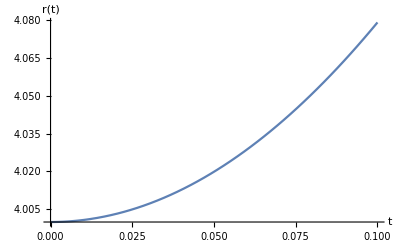

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t] ]  , { t, 0, 0.1 } , AxesLabel->{ t  ,  q[[1]] }   ]
```

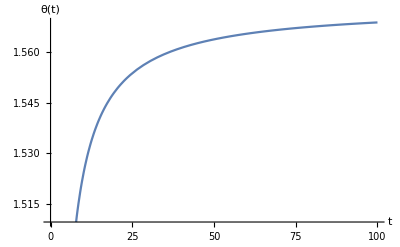

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t] ]  , { t, 0, 100 } , AxesLabel->{ t  ,  q[[2]] }   ]
```